```mathematica
Subscript[F, 1][r_]:=Piecewise[{{Exp[-r^2/(2*σ^2)],0<r<w},{0,r>w||r<0}}];
```

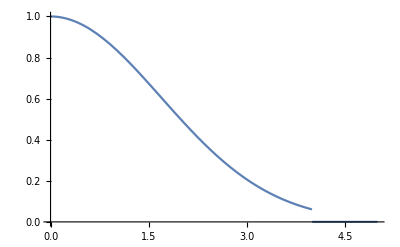

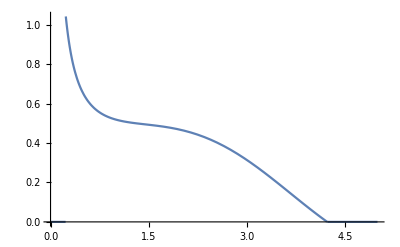

0.990028

```mathematica
σ=1.69;
w=4;
θ=10*Pi/180;
d = 24;

R[r_]:=d*Tan[θ]-r;
Subscript[F, 2][r_]:=Subscript[F, 1][R[r]]*R[r]/r;

Plot[Subscript[F, 1][r],{r,0,5},PlotRange->{0,1}]
Plot[Subscript[F, 2][r],{r,0,5},PlotRange->Full]

Subscript[P, in]=2*Pi*NIntegrate[r*Subscript[F, 1][r],{r,0,w}];
Subscript[P, out]=2*Pi*NIntegrate[r*Subscript[F, 2][r],{r,0,w}];
Efficiency=Subscript[P, out]/Subscript[P, in]
```

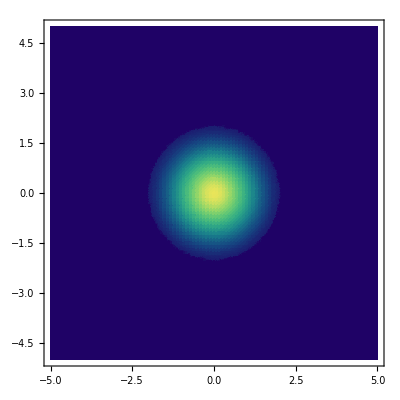

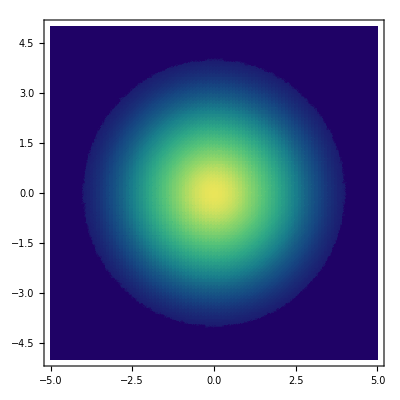

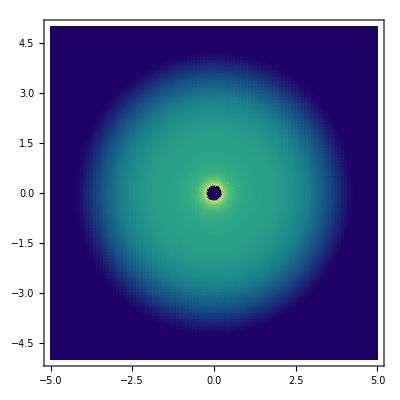

```mathematica
r[x_,y_]:=Sqrt[x^2+y^2];
DensityPlot[Subscript[F, 1][2*r[x,y]],{x,-5,5},{y,-5,5},ColorFunction->"BlueGreenYellow",Exclusions->None,PlotPoints->{100,100}]
DensityPlot[Subscript[F, 1][1*r[x,y]],{x,-5,5},{y,-5,5},ColorFunction->"BlueGreenYellow",Exclusions->None,PlotPoints->{100,100}]
DensityPlot[Subscript[F, 2][1*r[x,y]],{x,-5,5},{y,-5,5},ColorFunction->"BlueGreenYellow",Exclusions->None,PlotPoints->{100,100}]
```